# Fit of Gaussian TMD convolution 𝒞[f_1^g f_1^g] over LHCb 13 TeV data of dσ/dq_T for double J/ψ production ; extraction of <k_T^2> = R^2

## Initialisation

```mathematica
SetDirectory[NotebookDirectory[]];
```

Package used to plot error bars and bin bars

```mathematica
Needs["ErrorBarPlots`"]
```

Computation of the ratio S = dσ/(∫_0^(Q/2) dσ dq_T) = (q_T 𝒞[f_1^g f_1^g])/(∫_0^(Q/2) q_T 𝒞[f_1^g f_1^g] dq_T) with dσ ≡ dσ/(dQ dY dΩ dq_T) (result checked on paper + check that ∫_0^(Q/2) S dq_T = 1)

```mathematica
Cf1f1Gaus=1/(2π R^2) ⅇ^(-qt^2/(2 R^2));
```

```mathematica
Cf1f1Gausintqt=Integrate[qt*Cf1f1Gaus,{qt,0,Q/2},Assumptions->{Q∈Reals,R∈Reals,Q>0}]
```

-(-1+ⅇ^(-Q^2/(8 R^2)))/(2 π)

```mathematica
SGaus=(qt*Cf1f1Gaus)/Cf1f1Gausintqt//Simplify
```

-(ⅇ^(-qt^2/(2 R^2)) qt)/((-1+ⅇ^(-Q^2/(8 R^2))) R^2)

```mathematica
Integrate[SGaus,{qt,0,Q/2},Assumptions->{Q∈Reals,Q>0,R∈Reals,R>0}]
```

1

Computation of the ratio S binned over 1 GeV intervals (factor 2 at denominator omitted as it would be re-suppressed in the normalisation to 1)

```mathematica
SGausbin0p5=0.5*((SGaus/.qt->qt-0.5)+(SGaus/.qt->qt+0.5))//FullSimplify
```

(ⅇ^((-0.25+0.125 Q^2-1. qt^2)/R^2) (ⅇ^((0.5 (0.5+qt)^2)/R^2) (-0.25+0.5 qt)+ⅇ^((0.5 (-0.5+qt)^2)/R^2) (0.25+0.5 qt)))/((-1.+ⅇ^(Q^2/(8 R^2))) R^2)

Loading the LHCb data

```mathematica
MatrixForm[LHCb13dat=ReadList["LHCb13TeV_f1g2.dat",Number,RecordLists->True]];
```

Computing norm4, the sum over the first 4 data points ; these data points match the condition q_T< Q/2 necessary to ensure TMD applicability and will be the only points used for the fit.
The data are then normalised by dividing them by norm4

```mathematica
norm4=Sum[LHCb13dat[[i,2]],{i,1,4}]
```

9.04145

## No DPS subtraction

Fit of the S factor over the normalised LHCb data 
Q is taken as its average value in the data sample : Q ≃ 8 GeV
Each data point is weighted by the inverse square of its measurement uncertainty

```mathematica
fitLS4RsqGaus=NonlinearModelFit[Transpose[{LHCb13dat[[1;;4,1]],LHCb13dat[[1;;4,2]]/norm4}],SGausbin0p5/.R->√R2/.Q->8,R2,qt,Weights->1/(LHCb13dat[[1;;4,4]]/norm4)^2];
```

```mathematica
(* fitLS4RsqGaus=NonlinearModelFit[Transpose[{LHCb13dat[[1;;4,1]],LHCb13dat[[1;;4,2]]/norm4}],SGausbin0p5/.R->√R2/.Q->8,R2,qt, VarianceEstimatorFunction->(1&),Weights->1/(LHCb13dat[[1;;4,4]]/norm4)^2]; *)
```

Tables showing the results of the fit

```mathematica
fitLS4RsqGaus["ParameterTable"]
fitLS4RsqGaus["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
R2 | 4.90422 | 0.77883 | 6.29691 | 0.00809095

| Estimate | Standard Error | Confidence Interval
R2 | 4.90422 | 0.77883 | {2.42564,7.3828}

Evaluation of the reduced chisquare :
Weighted Sum of Squared Residuals : WSSR = ∑[(data(x)-fit(x))^2/error^2]
Number of Degrees of Freedom : ndf = number of data points - number of fit parameters (in our case, ndf=4-1=3)
reduced chisquare :  Rχ2 = WSSR/ndf

```mathematica
WSSR= ∑_(i=1)^4 (LHCb13dat[[i,2]]/norm4-fitLS4RsqGaus["BestFit"]/.qt->LHCb13dat[[i,1]])^2/(LHCb13dat[[i,4]]/norm4)^2;
ndf=3;
Rχ2=WSSR/ndf
```

0.415934

Plot of the normalised LHCb data with the resulting function given by the fit over the first 4 data points (here the uncertainty is taken to be half the width of the confidence interval) including the reduced χ^2 value

```mathematica
estLS4RsqGaus=(fitLS4RsqGaus["ParameterConfidenceIntervals"][[1,2]]+fitLS4RsqGaus["ParameterConfidenceIntervals"][[1,1]])/2;
errLS4RsqGaus=(fitLS4RsqGaus["ParameterConfidenceIntervals"][[1,2]]-fitLS4RsqGaus["ParameterConfidenceIntervals"][[1,1]])/2;
```

```mathematica
MatrixForm[LHCb13datPlot4=Table[{{LHCb13dat[[i,1]],LHCb13dat[[i,2]]/norm4},ErrorBar[LHCb13dat[[i,3]],LHCb13dat[[i,4]]/norm4]},{i,1,Length[LHCb13dat]}]];
```

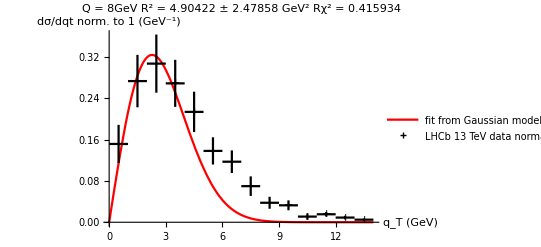

```mathematica
Show[Plot[fitLS4RsqGaus["BestFit"],{qt,0,14},PlotStyle->Red,PlotLegends->{"fit from Gaussian model over normalised data in region q_T<Q/2"}],ErrorListPlot[LHCb13datPlot4,PlotMarkers->"+",PlotStyle->Black,PlotLegends->{"LHCb 13 TeV data normalised over region q_T<Q/2"}],AxesLabel->{"q_T (GeV)","dσ/dqt norm. to 1 (GeV^-1)"},PlotRange->All,PlotLabel->Style["Q = 8GeV     R^2 = "<>ToString[estLS4RsqGaus]<>" ± "<>ToString[errLS4RsqGaus]<>" GeV^2     Rχ^2 = "<>ToString[Rχ2],FontSize->14]]
```

## With DPS subtraction, without binning

Loading the LHCb data with DPS subtracted

```mathematica
MatrixForm[LHCb13datNODPS=ReadList["LHCb13TeV_f1g2_noDPS.dat",Number,RecordLists->True]];
```

These data are already normalised

```mathematica
norm4NODPS=Sum[LHCb13datNODPS[[i,2]],{i,1,4}]
```

1.

Fit

```mathematica
fitLS4RsqGausNODPSNOBIN=NonlinearModelFit[Transpose[{LHCb13datNODPS[[1;;4,1]],LHCb13datNODPS[[1;;4,2]]/norm4NODPS}],SGaus/.R->√R2/.Q->8,R2,qt,Weights->1/(LHCb13datNODPS[[1;;4,4]]/norm4NODPS)^2];
```

```mathematica
fitLS4RsqGausNODPSNOBIN["ParameterTable"]
fitLS4RsqGausNODPSNOBIN["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
R2 | 3.73883 | 0.749438 | 4.98884 | 0.015487

| Estimate | Standard Error | Confidence Interval
R2 | 3.73883 | 0.749438 | {1.35378,6.12388}

```mathematica
WSSRNODPSNOBIN= ∑_(i=1)^4 (LHCb13datNODPS[[i,2]]/norm4NODPS-fitLS4RsqGausNODPSNOBIN["BestFit"]/.qt->LHCb13datNODPS[[i,1]])^2/(LHCb13datNODPS[[i,4]]/norm4NODPS)^2;
ndf=3;
Rχ2NODPSNOBIN=WSSRNODPSNOBIN/ndf
```

0.341354

```mathematica
estLS4RsqGausNODPSNOBIN=1/2(fitLS4RsqGausNODPSNOBIN["ParameterConfidenceIntervals"][[1,2]]+fitLS4RsqGausNODPSNOBIN["ParameterConfidenceIntervals"][[1,1]]);
errLS4RsqGausNODPSNOBIN=(fitLS4RsqGausNODPSNOBIN["ParameterConfidenceIntervals"][[1,2]]-fitLS4RsqGausNODPSNOBIN["ParameterConfidenceIntervals"][[1,1]])/2;
```

The DPS-subtracted data are narrower in q_T, resulting in a lower value for the fitted R^2

```mathematica
MatrixForm[LHCb13datNODPSPlot4=Table[{{LHCb13datNODPS[[i,1]],LHCb13datNODPS[[i,2]]/norm4NODPS},ErrorBar[LHCb13datNODPS[[i,3]],LHCb13datNODPS[[i,4]]/norm4NODPS]},{i,1,Length[LHCb13datNODPS]}]];
```

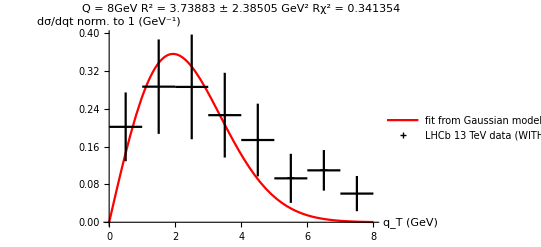

```mathematica
Show[Plot[fitLS4RsqGausNODPSNOBIN["BestFit"],{qt,0,8},PlotStyle->Red,PlotLegends->{"fit from Gaussian model over normalised data (DPS subtracted) in region q_T<Q/2"}],ErrorListPlot[LHCb13datNODPSPlot4,PlotMarkers->"+",PlotStyle->Black,PlotLegends->{"LHCb 13 TeV data (WITHOUT DPS) normalised over region q_T<Q/2"}],AxesLabel->{"q_T (GeV)","dσ/dqt norm. to 1 (GeV^-1)"},PlotRange->All,PlotLabel->Style["Q = 8GeV     R^2 = "<>ToString[estLS4RsqGausNODPSNOBIN]<>" ± "<>ToString[errLS4RsqGausNODPSNOBIN]<>" GeV^2     Rχ^2 = "<>ToString[Rχ2NODPSNOBIN],FontSize->14]]
```

## With DPS subtraction and binning

Computation of the ratio S binned over 1 GeV intervals with binning : average over bin [a,b] = av ; surface under curve (= integral) = H ; H=(b-a) x av => av = H/(b-a) = (∫_a^b y(x)ⅆx)/(b-a) = (Y_prim(b)-Y_prim(a))/(b-a)

```mathematica
SGaus
```

-(ⅇ^(-qt^2/(2 R^2)) qt)/((-1+ⅇ^(-Q^2/(8 R^2))) R^2)

Primitive of SGaus  (Y_prim in our explanation)

```mathematica
SGausint=∫SGaus ⅆqt
```

(ⅇ^(-qt^2/(2 R^2)))/(-1+ⅇ^(-Q^2/(8 R^2)))

```mathematica
SGausintfunc[x_]:=(ⅇ^(-x^2/(2 R^2)))/(-1+ⅇ^(-Q^2/(8 R^2)));
```

Binned value of SGaus : for any qt ∈ [a,b], we compute (Y_prim(b)-Y_prim(a))/(b-a) (since the bins are [n,n+1], a=IntegerPart[qt] and b=IntegerPart[qt]+1 and b-a=1)

```mathematica
SGausbincorr=SGausintfunc[IntegerPart[qt]+1]-SGausintfunc[IntegerPart[qt]]//FullSimplify
```

(ⅇ^(Q^2/(8 R^2)) (ⅇ^(-IntegerPart[qt]^2/(2 R^2))-ⅇ^(-(1+IntegerPart[qt])^2/(2 R^2))))/(-1+ⅇ^(Q^2/(8 R^2)))

```mathematica
SGausbincorrfunc[x_]:=(ⅇ^(Q^2/(8 R^2)) (ⅇ^(-IntegerPart[x]^2/(2 R^2))-ⅇ^(-(1+IntegerPart[x])^2/(2 R^2))))/(-1+ⅇ^(Q^2/(8 R^2)));
```

New fit gives a slightly lower R^2

```mathematica
fitLS4RsqGausNODPSBINCORR=NonlinearModelFit[Transpose[{LHCb13datNODPS[[1;;4,1]],LHCb13datNODPS[[1;;4,2]]/norm4NODPS}],SGausbincorrfunc[qt]/.R->√R2/.Q->8,R2,qt,Weights->1/(LHCb13datNODPS[[1;;4,4]]/norm4NODPS)^2];
```

```mathematica
fitLS4RsqGausNODPSBINCORR["ParameterTable"]
fitLS4RsqGausNODPSBINCORR["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
R2 | 3.63956 | 0.751957 | 4.84011 | 0.0168225

| Estimate | Standard Error | Confidence Interval
R2 | 3.63956 | 0.751957 | {1.24649,6.03262}

```mathematica
WSSRNODPSBINCORR= ∑_(i=1)^4 (LHCb13datNODPS[[i,2]]/norm4NODPS-fitLS4RsqGausNODPSBINCORR["BestFit"]/.qt->LHCb13datNODPS[[i,1]])^2/(LHCb13datNODPS[[i,4]]/norm4NODPS)^2;
ndf=3;
Rχ2NODPSBINCORR=WSSRNODPSBINCORR/ndf
```

0.33504

```mathematica
estLS4RsqGausNODPSBINCORR=1/2(fitLS4RsqGausNODPSBINCORR["ParameterConfidenceIntervals"][[1,2]]+fitLS4RsqGausNODPSBINCORR["ParameterConfidenceIntervals"][[1,1]]);
errLS4RsqGausNODPSBINCORR=(fitLS4RsqGausNODPSBINCORR["ParameterConfidenceIntervals"][[1,2]]-fitLS4RsqGausNODPSBINCORR["ParameterConfidenceIntervals"][[1,1]])/2;
```

```mathematica
MatrixForm[LHCb13datNODPSPlot4=Table[{{LHCb13datNODPS[[i,1]],LHCb13datNODPS[[i,2]]/norm4NODPS},ErrorBar[LHCb13datNODPS[[i,3]],LHCb13datNODPS[[i,4]]/norm4NODPS]},{i,1,Length[LHCb13datNODPS]}]];
```

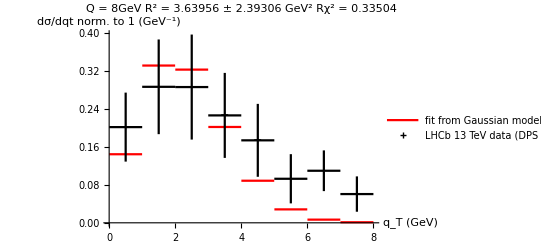

```mathematica
Show[Plot[fitLS4RsqGausNODPSBINCORR["BestFit"],{qt,0,8},PlotStyle->Red,PlotLegends->{"fit from Gaussian model (with binning) over normalised data (DPS subtracted) in region q_T<Q/2"}],ErrorListPlot[LHCb13datNODPSPlot4,PlotMarkers->"+",PlotStyle->Black,PlotLegends->{"LHCb 13 TeV data (DPS subtracted) normalised over region q_T<Q/2"}],AxesLabel->{"q_T (GeV)","dσ/dqt norm. to 1 (GeV^-1)"},PlotRange->All,PlotLabel->Style["Q = 8GeV     R^2 = "<>ToString[estLS4RsqGausNODPSBINCORR]<>" ± "<>ToString[errLS4RsqGausNODPSBINCORR]<>" GeV^2     Rχ^2 = "<>ToString[Rχ2NODPSBINCORR],FontSize->14]]
```